```mathematica
ClearAll["Global`*"]
```

```mathematica
a = {1,100000000};
a0 = Total[a];
mu = {-15,-15};
sig = {1,1.21};
nprey = Length[a];

VarZ =N[Sum[a[[i]]/a0(sig[[i]]^2+mu[[i]]^2) - (a[[i]]^2 *mu[[i]]^2)/a0^2,{i,1,nprey}] - Sum[(a[[i]]*a[[j]]*mu[[i]]*mu[[j]])/a0^2 Boole[i≠j],{i,1,nprey},{j,1,nprey}]]
```

1.4641

```mathematica
1.21^2
```

1.4641

```mathematica
Manipulate[
VarZ=Table[
a = {1,a2,1};
a0 = Total[a];
mu = {-15,mean2,-15};
sig = {1,500,1};
nprey = Length[a];
{a2/a0,N[Sum[a[[i]]/a0(sig[[i]]^2+mu[[i]]^2) - (a[[i]]^2 *mu[[i]]^2)/a0^2,{i,1,nprey}] - Sum[(a[[i]]*a[[j]]*mu[[i]]*mu[[j]])/a0^2 Boole[i≠j],{i,1,nprey},{j,1,nprey}]]},
{a2,1,100,0.1}];
Show[{
ListPlot[VarZ,PlotRange->{{0,1},{0,100}},Joined->True],
Graphics[Line[{{0,Max[VarZ[[All,2]]]},{1,Max[VarZ[[All,2]]]}}]]
}]
,{mean2,-15,0}]
```

```mathematica
VarZ[[All,2]]
```

```mathematica
VarZ=(1-s)/(n-1)*A + s*B - ((1-s)/(n-1)*c + s*d)^2
Ds = D[VarZ,s]
```

(A (1-s))/(-1+n)+B s-((c (1-s))/(-1+n)+d s)^2

B-A/(-1+n)-2 (d-c/(-1+n)) ((c (1-s))/(-1+n)+d s)

```mathematica
Ssol2 = s/.FullSimplify[Solve[Ds==0,s]]
```

{(A+B (-1+n)^2-A n+2 c (c+d-d n))/(2 (c+d-d n)^2)}

```mathematica
S=((A/(n-1)-B)/(2*(c/(n-1)-d))- 1/(n-1))/(d -c/(n-1))
```

((-B+A/(-1+n))/(2 (-d+c/(-1+n)))-1/(-1+n))/(d-c/(-1+n))

```mathematica
Ssol =FullSimplify[S]
```

(A+B+2 (c+d)-(A+2 (B+d)) n+B n^2)/(2 (c+d-d n)^2)

Analysis of Inflexion point

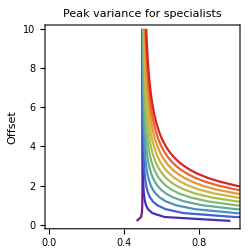
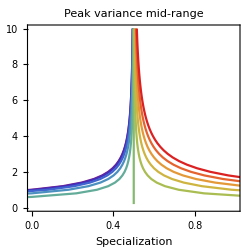
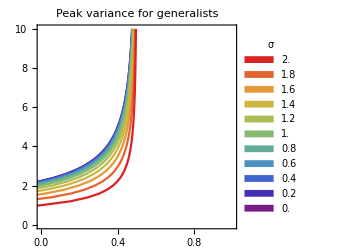
-Graphics- | -Graphics- | -Graphics-

```mathematica
VarSpecFig =Grid[{
Flatten[{
mtable=
Table[
Table[
mu = {-15,-15+offset,-15};
sig = {0.05,s2,0.05};
nprey = Length[mu];
prey1 = 2;
FullSsol = Ssol2/.{
n->nprey,
A->Sum[(sig[[i]]^2 + mu[[i]]^2)Boole[i≠prey1],{i,1,nprey}],
B->(sig[[prey1]]^2 + mu[[prey1]]^2),
c->Sum[mu[[i]]Boole[i≠prey1],{i,1,nprey}],
d-> mu[[prey1]]
};
Flatten[{N[FullSsol],offset}],
{offset,0.2,10,0.2}],
{s2,0,2,0.2}];
ListPlot[mtable,Joined->True,Frame->True,PlotStyle->"Rainbow",PlotRange->{{0,1},All},ImageSize->250,FrameLabel->{"","Offset"},AspectRatio->1,PlotLabel->"Peak variance for specialists"],
mtable=
Table[
Table[
mu = {-15,-15+offset,-15};
sig = {1,s2,1};
nprey = Length[mu];
prey1 = 2;
FullSsol = Ssol2/.{
n->nprey,
A->Sum[(sig[[i]]^2 + mu[[i]]^2)Boole[i≠prey1],{i,1,nprey}],
B->(sig[[prey1]]^2 + mu[[prey1]]^2),
c->Sum[mu[[i]]Boole[i≠prey1],{i,1,nprey}],
d-> mu[[prey1]]
};
Flatten[{N[FullSsol],offset}],
{offset,0.2,10,0.2}],
{s2,0,2,0.2}];
ListPlot[mtable,Joined->True,Frame->True,PlotStyle->"Rainbow",PlotRange->{{0,1},All},ImageSize->250,
FrameLabel->{"Specialization",""},PlotLabel->"Peak variance mid-range",AspectRatio->1],
mtable=
Table[
Table[
mu = {-15,-15+offset,-15};
sig = {1,s2,3};
nprey = Length[mu];
prey1 = 2;
FullSsol = Ssol2/.{
n->nprey,
A->Sum[(sig[[i]]^2 + mu[[i]]^2)Boole[i≠prey1],{i,1,nprey}],
B->(sig[[prey1]]^2 + mu[[prey1]]^2),
c->Sum[mu[[i]]Boole[i≠prey1],{i,1,nprey}],
d-> mu[[prey1]]
};
Flatten[{N[FullSsol],offset}],
{offset,0.2,10,0.2}],
{s2,0,2,0.2}];
ListPlot[mtable,Joined->True,Frame->True,PlotStyle->"Rainbow",PlotRange->{{0,1},All},FrameLabel->{"",""},PlotLegends->SwatchLegend[Table[σ,{σ,0,2,0.2}],LegendLabel->"σ",LegendFunction->(#&),LegendMargins->1,LegendLayout->{"ReversedColumn",1}],ImageSize->250,AspectRatio->1,PlotLabel->"Peak variance for generalists"]
}]
}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_specvar.pdf",VarSpecFig]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_specvar.pdf

0) Parabola is always upside down... there is always a ‘peak variance’... often it is within specialization= [0,1]
1) Distribution of variances determines whether the peak is on the left (generalists have higher variance) or on the right (specialists have higher variances)
2) Across offset values for the ‘specialized prey’, the peak tends to be in the middle; this means the moderate specialist has higher variance